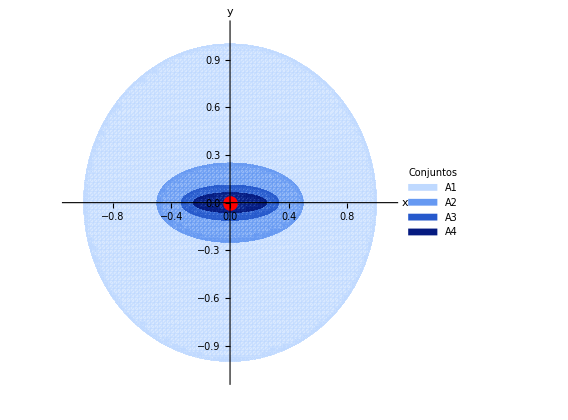

```mathematica
nMax=4;
colores={RGBColor[0.75,0.85,1],RGBColor[0.4,0.6,0.95],RGBColor[0.15,0.35,0.8],RGBColor[0.02,0.1,0.5]};
etiquetas={"A1","A2","A3","A4"};

grafico=Show[Table[RegionPlot[n^2 x^2+n^4 y^2<=1,{x,-1.1,1.1},{y,-1.1,1.1},PlotStyle->Directive[colores[[n]],Opacity[0.6]],BoundaryStyle->None,PlotPoints->80],{n,1,nMax}],Graphics[{Red,PointSize[0.025],Point[{0,0}]}],Axes->True,AxesOrigin->{0,0},AxesLabel->{Style["x",18],Style["y",18]},TicksStyle->Directive[FontSize->14],Frame->False,AspectRatio->1,ImageSize->420];

Legended[grafico,SwatchLegend[colores,etiquetas,LegendLabel->Style["Conjuntos",16],LabelStyle->Directive[FontSize->16],LegendMarkerSize->18]]
```

```mathematica
Export["C:\\Users\\jesus\\Desktop\\Universidad\\Teoría de la probabilidad\\Latex_Teoria_Probabilidad\\imagenes\\problemas_Quesada\\prob_quesada_1_18_a.png",%26,"PNG"]
```

C:\Users\jesus\Desktop\Universidad\Teoría de la probabilidad\Latex_Teoria_Probabilidad\imagenes\problemas_Quesada\prob_quesada_1_18_a.png

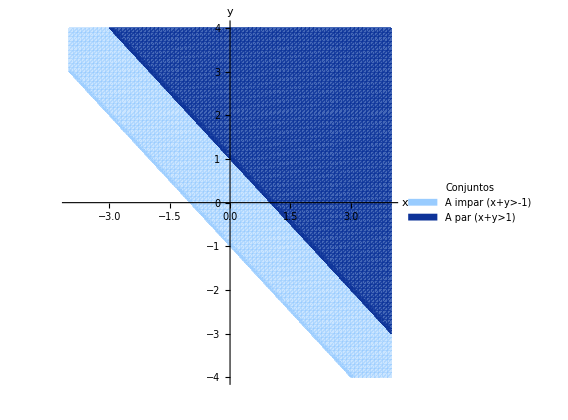

```mathematica
rango=4;
coloresB={RGBColor[0.6,0.8,1],RGBColor[0.05,0.2,0.6]};
etiquetasB={"A impar (x+y>-1)","A par (x+y>1)"};

graficoB=Show[RegionPlot[x+y>-1,{x,-rango,rango},{y,-rango,rango},PlotStyle->Directive[coloresB[[1]],Opacity[0.5]],BoundaryStyle->None,PlotPoints->80],RegionPlot[x+y>1,{x,-rango,rango},{y,-rango,rango},PlotStyle->Directive[coloresB[[2]],Opacity[0.7]],BoundaryStyle->None,PlotPoints->80],Axes->True,AxesOrigin->{0,0},AxesLabel->{Style["x",18],Style["y",18]},TicksStyle->Directive[FontSize->14],Frame->False,AspectRatio->1,ImageSize->420];

Legended[graficoB,SwatchLegend[coloresB,etiquetasB,LegendLabel->Style["Conjuntos",16],LabelStyle->Directive[FontSize->16],LegendMarkerSize->18]]
```

```mathematica
Export["C:\\Users\\jesus\\Desktop\\Universidad\\Teoría de la probabilidad\\Latex_Teoria_Probabilidad\\imagenes\\problemas_Quesada\\prob_quesada_1_18_b.png",%31,"PNG"]
```

C:\Users\jesus\Desktop\Universidad\Teoría de la probabilidad\Latex_Teoria_Probabilidad\imagenes\problemas_Quesada\prob_quesada_1_18_b.png